# Fix Control laser

## Analy

```mathematica
Rbpress[T_]:=
(*
Calculates the vapor pressure of Na depending on the temprerature of the cell.;
Input variable: T:temperature[C];
Output variable: p=Na pressure[torr];
Formulas obtained from "Sodium D Line Data" by Daniel A.Steck;
http://steck.us/alkalidata
*)

Module[{T1,p,k,c,MRb,w0,Nat,dopp},
T1=T+273.15;
(*If[T1<39.31+273.15,p=10^(-94.04826-1961.258/T1-0.03771687*T1+42.57526*Log[10,T1])
,p=10^(15.88253-4529.635/T1+0.00058663*T1-2.99138*Log[10,T1])
];*)
p= If[T1<312.5,10^(9.863-4215/T1),10^(9.318-4040/T1)];(*Unit is in Pa*)
k=1.3806503 10^-23; (*Boltzman's contstant[J/K]*)
c=2.99792458 10^8;(*Speed of light[m/s]*)
MRb=1.409993119 10^-25;(*Rb 85 atomic mass[kg]*)
(*w0=2Pi 377.107385*10^12;(*Transition frequency for 85Rb D1 line*)
dopp=w0/c*Sqrt[2 k*T1/MRb];*)
w0=794.76728224*10^-9;(*Transition frequency for 85Rb D1 line*)
dopp=2Pi/w0*Sqrt[2k*T1/MRb];
Nat=p/(k*T1); (*units in m^-3*)

{Nat,dopp,p,Sqrt[3k*T1/MRb]}
]
```

```mathematica
Lev4Testsc[T_,P_,diam_,gam_,delt_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41,Δ2},
d=Range[-0.8,0.4,0.001]*10^9;
Δ=2Pi delt;
δ=2Pi d;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(d42^2 Nat ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(2 √5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ32=-(d32^2 Nat ((-35+2 √70) omegac1^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)))/(5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ24=(d42^2 Nat (ⅈ (4 √5-5 √14) omegac1^2+16 √5 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)))/(2 √5 e0 (8 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ) (w43+ⅈ γ42+δ+Δ)+ⅈ omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)) ℏ);
χ23=(d32^2 Nat ((35 √2-4 √35) omegac1^2-40 ⅈ √2 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ)))/(5 √2 e0 (omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))) ℏ);

Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]

]
```

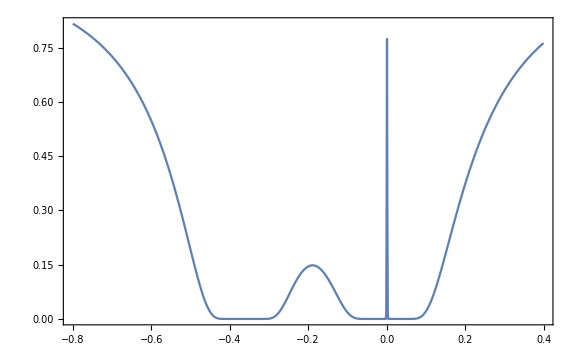

```mathematica
ListPlot[Lev4Testsc[100,15/1000,1/1000,0,0],Joined->True,PlotRange->All,Frame->True,Axes->False,ImageSize->Large]
```

## Numerical

```mathematica
Table[((M9/.Flatten[Table[{Subscript[σ, i,j][t]->Subscript[σ, i,j],Subscript[γ, i,j]->ToExpression["γ"<>ToString[i]<>ToString[j]]},{i,1,4},{j,1,4}]])/.{Subscript[σ, 1,1]->0,Subscript[σ, 2,2]->1,Subscript[σ, 3,3]->0,Subscript[σ, 4,4]->0})[[{2,3,4,5,7,8,9,10,12,13,14,15},2]][[i]]==0,{i,1,12}]
```

{-γ12 σ_(1,2)-ⅈ δ σ_(1,2)-1/2 ⅈ Ω32 σ_(1,3)-(ⅈ Ω32 σ_(1,4))/(√5)+1/2 ⅈ Ω13 σ_(3,2)+1/2 ⅈ √(7/2) Ω13 σ_(4,2)==0,-1/2 ⅈ Ω23 σ_(1,2)-γ13 σ_(1,3)+ⅈ Δ1 σ_(1,3)+1/2 ⅈ √(7/2) Ω13 σ_(4,3)==0,-(ⅈ Ω23 σ_(1,2))/(√5)+ⅈ w43 σ_(1,4)-γ14 σ_(1,4)+ⅈ Δ1 σ_(1,4)+1/2 ⅈ Ω13 σ_(3,4)==0,-γ21 σ_(2,1)+ⅈ δ σ_(2,1)-1/2 ⅈ Ω31 σ_(2,3)-1/2 ⅈ √(7/2) Ω31 σ_(2,4)+1/2 ⅈ Ω23 σ_(3,1)+(ⅈ Ω23 σ_(4,1))/(√5)==0,-(ⅈ Ω23)/2-1/2 ⅈ Ω13 σ_(2,1)-γ23 σ_(2,3)+ⅈ δ σ_(2,3)+ⅈ Δ1 σ_(2,3)+(ⅈ Ω23 σ_(4,3))/(√5)==0,-(ⅈ Ω23)/(√5)-1/2 ⅈ √(7/2) Ω13 σ_(2,1)+ⅈ w43 σ_(2,4)-γ24 σ_(2,4)+ⅈ δ σ_(2,4)+ⅈ Δ1 σ_(2,4)+1/2 ⅈ Ω23 σ_(3,4)==0,1/2 ⅈ Ω32 σ_(2,1)-γ31 σ_(3,1)-ⅈ Δ1 σ_(3,1)-1/2 ⅈ √(7/2) Ω31 σ_(3,4)==0,(ⅈ Ω32)/2+1/2 ⅈ Ω31 σ_(1,2)-γ32 σ_(3,2)-ⅈ δ σ_(3,2)-ⅈ Δ1 σ_(3,2)-(ⅈ Ω32 σ_(3,4))/(√5)==0,1/2 ⅈ Ω31 σ_(1,4)+1/2 ⅈ Ω32 σ_(2,4)-1/2 ⅈ √(7/2) Ω13 σ_(3,1)-(ⅈ Ω23 σ_(3,2))/(√5)+ⅈ w43 σ_(3,4)-γ34 σ_(3,4)==0,(ⅈ Ω32 σ_(2,1))/(√5)-ⅈ w43 σ_(4,1)-γ41 σ_(4,1)-ⅈ Δ1 σ_(4,1)-1/2 ⅈ Ω31 σ_(4,3)==0,(ⅈ Ω32)/(√5)+1/2 ⅈ √(7/2) Ω31 σ_(1,2)-ⅈ w43 σ_(4,2)-γ42 σ_(4,2)-ⅈ δ σ_(4,2)-ⅈ Δ1 σ_(4,2)-1/2 ⅈ Ω32 σ_(4,3)==0,1/2 ⅈ √(7/2) Ω31 σ_(1,3)+(ⅈ Ω32 σ_(2,3))/(√5)-1/2 ⅈ Ω13 σ_(4,1)-1/2 ⅈ Ω23 σ_(4,2)-ⅈ w43 σ_(4,3)-γ43 σ_(4,3)==0}

```mathematica
Lev4TestscNum[T_,Pp_,diamp_,Pc_,diamc_,gam_,delt_] :=Module[{Δ1,Δ2,Δ,δ,Nat,γ21,γ12,d32,d42,d31,d41,ℏ,e0,c,wcn,wc,u,omegac1,omegac2,γ34,γ43,w43,Ω13,Ω31,Ω23,Ω32,γ23,γ32,γ13,γ31,γ41,γ14,γ24,γ42,M10,s42,s32},
Δ1=2Pi delt;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ12=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
γ23=2*Pi*5.750056 10^6/2;
γ24=2*Pi*5.750056 10^6/2;
γ31=2*Pi*5.750056 10^6/2;
γ41=2*Pi*5.750056 10^6/2;
γ13=2*Pi*5.750056 10^6/2;
γ14=2*Pi*5.750056 10^6/2;
γ34=2*Pi*5.750056 10^6;
γ43=2*Pi*5.750056 10^6;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 
Ω23=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[Pp/(Pi*(diamp/2)^2)]); 
Ω32=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[Pp/(Pi*(diamp/2)^2)]); 
Ω13=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[Pc/(Pi*(diamc/2)^2)]); 
Ω31=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[Pc/(Pi*(diamc/2)^2)]); 

M10={-γ12 Subscript[σ, 1,2]-ⅈ δ Subscript[σ, 1,2]-1/2 ⅈ Ω32 Subscript[σ, 1,3]-(ⅈ Ω32 Subscript[σ, 1,4])/(√5)+1/2 ⅈ Ω13 Subscript[σ, 3,2]+1/2 ⅈ √(7/2) Ω13 Subscript[σ, 4,2]==0,-1/2 ⅈ Ω23 Subscript[σ, 1,2]-γ13 Subscript[σ, 1,3]+ⅈ Δ1 Subscript[σ, 1,3]+1/2 ⅈ √(7/2) Ω13 Subscript[σ, 4,3]==0,-(ⅈ Ω23 Subscript[σ, 1,2])/(√5)+ⅈ w43 Subscript[σ, 1,4]-γ14 Subscript[σ, 1,4]+ⅈ Δ1 Subscript[σ, 1,4]+1/2 ⅈ Ω13 Subscript[σ, 3,4]==0,-γ21 Subscript[σ, 2,1]+ⅈ δ Subscript[σ, 2,1]-1/2 ⅈ Ω31 Subscript[σ, 2,3]-1/2 ⅈ √(7/2) Ω31 Subscript[σ, 2,4]+1/2 ⅈ Ω23 Subscript[σ, 3,1]+(ⅈ Ω23 Subscript[σ, 4,1])/(√5)==0,-(ⅈ Ω23)/2-1/2 ⅈ Ω13 Subscript[σ, 2,1]-γ23 Subscript[σ, 2,3]+ⅈ δ Subscript[σ, 2,3]+ⅈ Δ1 Subscript[σ, 2,3]+(ⅈ Ω23 Subscript[σ, 4,3])/(√5)==0,-(ⅈ Ω23)/(√5)-1/2 ⅈ √(7/2) Ω13 Subscript[σ, 2,1]+ⅈ w43 Subscript[σ, 2,4]-γ24 Subscript[σ, 2,4]+ⅈ δ Subscript[σ, 2,4]+ⅈ Δ1 Subscript[σ, 2,4]+1/2 ⅈ Ω23 Subscript[σ, 3,4]==0,1/2 ⅈ Ω32 Subscript[σ, 2,1]-γ31 Subscript[σ, 3,1]-ⅈ Δ1 Subscript[σ, 3,1]-1/2 ⅈ √(7/2) Ω31 Subscript[σ, 3,4]==0,(ⅈ Ω32)/2+1/2 ⅈ Ω31 Subscript[σ, 1,2]-γ32 Subscript[σ, 3,2]-ⅈ δ Subscript[σ, 3,2]-ⅈ Δ1 Subscript[σ, 3,2]-(ⅈ Ω32 Subscript[σ, 3,4])/(√5)==0,1/2 ⅈ Ω31 Subscript[σ, 1,4]+1/2 ⅈ Ω32 Subscript[σ, 2,4]-1/2 ⅈ √(7/2) Ω13 Subscript[σ, 3,1]-(ⅈ Ω23 Subscript[σ, 3,2])/(√5)+ⅈ w43 Subscript[σ, 3,4]-γ34 Subscript[σ, 3,4]==0,(ⅈ Ω32 Subscript[σ, 2,1])/(√5)-ⅈ w43 Subscript[σ, 4,1]-γ41 Subscript[σ, 4,1]-ⅈ Δ1 Subscript[σ, 4,1]-1/2 ⅈ Ω31 Subscript[σ, 4,3]==0,(ⅈ Ω32)/(√5)+1/2 ⅈ √(7/2) Ω31 Subscript[σ, 1,2]-ⅈ w43 Subscript[σ, 4,2]-γ42 Subscript[σ, 4,2]-ⅈ δ Subscript[σ, 4,2]-ⅈ Δ1 Subscript[σ, 4,2]-1/2 ⅈ Ω32 Subscript[σ, 4,3]==0,1/2 ⅈ √(7/2) Ω31 Subscript[σ, 1,3]+(ⅈ Ω32 Subscript[σ, 2,3])/(√5)-1/2 ⅈ Ω13 Subscript[σ, 4,1]-1/2 ⅈ Ω23 Subscript[σ, 4,2]-ⅈ w43 Subscript[σ, 4,3]-γ43 Subscript[σ, 4,3]==0};

Table[
{s32,s42}=Solve[M10/.δ-> 2Pi d*10^9,{Subscript[σ, 1,2],Subscript[σ, 1,3],Subscript[σ, 1,4],Subscript[σ, 2,1],Subscript[σ, 2,3],Subscript[σ, 2,4],Subscript[σ, 3,1],Subscript[σ, 3,2],Subscript[σ, 3,4],Subscript[σ, 4,1],Subscript[σ, 4,2],Subscript[σ, 4,3]}][[1,{8,11},2]];
{d,Exp[-2Pi*0.0254/(2wcn)Im[((2 Nat d42^2)/(Sqrt[4/5]e0 ℏ Ω32)s42+(2 Nat d32^2)/(e0 ℏ Ω32)s32)]]}

,{d,-0.8,0.4,0.0005}]
]
```

```mathematica
Manipulate[
ListPlot[{Lev4TestscNum[T,Pp/1000000,0.5/1000,Pc/1000,1/1000,γtest 10^6,δtest 10^6],Lev4Testsc[T,Pc/1000,1/1000,γtest 10^6,δtest 10^6]},Joined->True,PlotRange->All,Frame->True,PlotStyle->{Black, {Red,Dashed}},Axes->False,ImageSize->1020,PlotLegends->{"Numerical","Analy"}]
,{T,50,100},{{Pp,30,"P prob (uW)"},0.00001,100},{{Pc,20,"Pcontrol (mW)"},0,100},{{γtest,1.5,"γ21 (GHz)"},0,5},{{δtest,0,"δ (GHz)"},-5,5}]
```

# Scan together

## Analy

```mathematica
Rbpress[T_]:=
(*
Calculates the vapor pressure of Na depending on the temprerature of the cell.;
Input variable: T:temperature[C];
Output variable: p=Na pressure[torr];
Formulas obtained from "Sodium D Line Data" by Daniel A.Steck;
http://steck.us/alkalidata
*)

Module[{T1,p,k,c,MRb,w0,Nat,dopp},
T1=T+273.15;
(*If[T1<39.31+273.15,p=10^(-94.04826-1961.258/T1-0.03771687*T1+42.57526*Log[10,T1])
,p=10^(15.88253-4529.635/T1+0.00058663*T1-2.99138*Log[10,T1])
];*)
p= If[T1<312.5,10^(9.863-4215/T1),10^(9.318-4040/T1)];(*Unit is in Pa*)
k=1.3806503 10^-23; (*Boltzman's contstant[J/K]*)
c=2.99792458 10^8;(*Speed of light[m/s]*)
MRb=1.409993119 10^-25;(*Rb 85 atomic mass[kg]*)
(*w0=2Pi 377.107385*10^12;(*Transition frequency for 85Rb D1 line*)
dopp=w0/c*Sqrt[2 k*T1/MRb];*)
w0=794.76728224*10^-9;(*Transition frequency for 85Rb D1 line*)
dopp=2Pi/w0*Sqrt[2k*T1/MRb];
Nat=p/(k*T1); (*units in m^-3*)

{Nat,dopp,p,Sqrt[3k*T1/MRb]}
]
```

```mathematica
Lev4Testsc[T_,P_,diam_,gam_,delt_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41,Δ2},
d=Range[-0.8,0.4,0.001]*10^9;
Δ=2Pi delt;
δ=2Pi d;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(d42^2 Nat ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(2 √5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ32=-(d32^2 Nat ((-35+2 √70) omegac1^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)))/(5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ24=(d42^2 Nat (ⅈ (4 √5-5 √14) omegac1^2+16 √5 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)))/(2 √5 e0 (8 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ) (w43+ⅈ γ42+δ+Δ)+ⅈ omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)) ℏ);
χ23=(d32^2 Nat ((35 √2-4 √35) omegac1^2-40 ⅈ √2 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ)))/(5 √2 e0 (omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))) ℏ);

Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]

]
```

```mathematica
ListPlot[Lev4Testsc[100,15/1000,1/1000,0,0],Joined->True,PlotRange->All,Frame->True,Axes->False,ImageSize->Large]
```

-Graphics-

## Numerical

```mathematica
Table[((M9/.Flatten[Table[{Subscript[σ, i,j][t]->Subscript[σ, i,j],Subscript[γ, i,j]->ToExpression["γ"<>ToString[i]<>ToString[j]]},{i,1,4},{j,1,4}]])/.{Subscript[σ, 1,1]->0,Subscript[σ, 2,2]->1,Subscript[σ, 3,3]->0,Subscript[σ, 4,4]->0})[[{2,3,4,5,7,8,9,10,12,13,14,15},2]][[i]]==0,{i,1,12}]
```

{-γ12 σ_(1,2)-ⅈ δ σ_(1,2)-1/2 ⅈ Ω32 σ_(1,3)-(ⅈ Ω32 σ_(1,4))/(√5)+1/2 ⅈ Ω13 σ_(3,2)+1/2 ⅈ √(7/2) Ω13 σ_(4,2)==0,-1/2 ⅈ Ω23 σ_(1,2)-γ13 σ_(1,3)+ⅈ Δ1 σ_(1,3)+1/2 ⅈ √(7/2) Ω13 σ_(4,3)==0,-(ⅈ Ω23 σ_(1,2))/(√5)+ⅈ w43 σ_(1,4)-γ14 σ_(1,4)+ⅈ Δ1 σ_(1,4)+1/2 ⅈ Ω13 σ_(3,4)==0,-γ21 σ_(2,1)+ⅈ δ σ_(2,1)-1/2 ⅈ Ω31 σ_(2,3)-1/2 ⅈ √(7/2) Ω31 σ_(2,4)+1/2 ⅈ Ω23 σ_(3,1)+(ⅈ Ω23 σ_(4,1))/(√5)==0,-(ⅈ Ω23)/2-1/2 ⅈ Ω13 σ_(2,1)-γ23 σ_(2,3)+ⅈ δ σ_(2,3)+ⅈ Δ1 σ_(2,3)+(ⅈ Ω23 σ_(4,3))/(√5)==0,-(ⅈ Ω23)/(√5)-1/2 ⅈ √(7/2) Ω13 σ_(2,1)+ⅈ w43 σ_(2,4)-γ24 σ_(2,4)+ⅈ δ σ_(2,4)+ⅈ Δ1 σ_(2,4)+1/2 ⅈ Ω23 σ_(3,4)==0,1/2 ⅈ Ω32 σ_(2,1)-γ31 σ_(3,1)-ⅈ Δ1 σ_(3,1)-1/2 ⅈ √(7/2) Ω31 σ_(3,4)==0,(ⅈ Ω32)/2+1/2 ⅈ Ω31 σ_(1,2)-γ32 σ_(3,2)-ⅈ δ σ_(3,2)-ⅈ Δ1 σ_(3,2)-(ⅈ Ω32 σ_(3,4))/(√5)==0,1/2 ⅈ Ω31 σ_(1,4)+1/2 ⅈ Ω32 σ_(2,4)-1/2 ⅈ √(7/2) Ω13 σ_(3,1)-(ⅈ Ω23 σ_(3,2))/(√5)+ⅈ w43 σ_(3,4)-γ34 σ_(3,4)==0,(ⅈ Ω32 σ_(2,1))/(√5)-ⅈ w43 σ_(4,1)-γ41 σ_(4,1)-ⅈ Δ1 σ_(4,1)-1/2 ⅈ Ω31 σ_(4,3)==0,(ⅈ Ω32)/(√5)+1/2 ⅈ √(7/2) Ω31 σ_(1,2)-ⅈ w43 σ_(4,2)-γ42 σ_(4,2)-ⅈ δ σ_(4,2)-ⅈ Δ1 σ_(4,2)-1/2 ⅈ Ω32 σ_(4,3)==0,1/2 ⅈ √(7/2) Ω31 σ_(1,3)+(ⅈ Ω32 σ_(2,3))/(√5)-1/2 ⅈ Ω13 σ_(4,1)-1/2 ⅈ Ω23 σ_(4,2)-ⅈ w43 σ_(4,3)-γ43 σ_(4,3)==0}

```mathematica
Lev4TestscNum[T_,Pp_,diamp_,Pc_,diamc_,gam_,delt_] :=Module[{Δ1,Δ2,Δ,δ,Nat,γ21,γ12,d32,d42,d31,d41,ℏ,e0,c,wcn,wc,u,omegac1,omegac2,γ34,γ43,w43,Ω13,Ω31,Ω23,Ω32,γ23,γ32,γ13,γ31,γ41,γ14,γ24,γ42,M10,s42,s32},
Δ1=2Pi delt;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ12=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
γ23=2*Pi*5.750056 10^6/2;
γ24=2*Pi*5.750056 10^6/2;
γ31=2*Pi*5.750056 10^6/2;
γ41=2*Pi*5.750056 10^6/2;
γ13=2*Pi*5.750056 10^6/2;
γ14=2*Pi*5.750056 10^6/2;
γ34=2*Pi*5.750056 10^6;
γ43=2*Pi*5.750056 10^6;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 
Ω23=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[Pp/(Pi*(diamp/2)^2)]); 
Ω32=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[Pp/(Pi*(diamp/2)^2)]); 
Ω13=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[Pc/(Pi*(diamc/2)^2)]); 
Ω31=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[Pc/(Pi*(diamc/2)^2)]); 

M10={-γ12 Subscript[σ, 1,2]-ⅈ δ Subscript[σ, 1,2]-1/2 ⅈ Ω32 Subscript[σ, 1,3]-(ⅈ Ω32 Subscript[σ, 1,4])/(√5)+1/2 ⅈ Ω13 Subscript[σ, 3,2]+1/2 ⅈ √(7/2) Ω13 Subscript[σ, 4,2]==0,-1/2 ⅈ Ω23 Subscript[σ, 1,2]-γ13 Subscript[σ, 1,3]+ⅈ Δ1 Subscript[σ, 1,3]+1/2 ⅈ √(7/2) Ω13 Subscript[σ, 4,3]==0,-(ⅈ Ω23 Subscript[σ, 1,2])/(√5)+ⅈ w43 Subscript[σ, 1,4]-γ14 Subscript[σ, 1,4]+ⅈ Δ1 Subscript[σ, 1,4]+1/2 ⅈ Ω13 Subscript[σ, 3,4]==0,-γ21 Subscript[σ, 2,1]+ⅈ δ Subscript[σ, 2,1]-1/2 ⅈ Ω31 Subscript[σ, 2,3]-1/2 ⅈ √(7/2) Ω31 Subscript[σ, 2,4]+1/2 ⅈ Ω23 Subscript[σ, 3,1]+(ⅈ Ω23 Subscript[σ, 4,1])/(√5)==0,-(ⅈ Ω23)/2-1/2 ⅈ Ω13 Subscript[σ, 2,1]-γ23 Subscript[σ, 2,3]+ⅈ δ Subscript[σ, 2,3]+ⅈ Δ1 Subscript[σ, 2,3]+(ⅈ Ω23 Subscript[σ, 4,3])/(√5)==0,-(ⅈ Ω23)/(√5)-1/2 ⅈ √(7/2) Ω13 Subscript[σ, 2,1]+ⅈ w43 Subscript[σ, 2,4]-γ24 Subscript[σ, 2,4]+ⅈ δ Subscript[σ, 2,4]+ⅈ Δ1 Subscript[σ, 2,4]+1/2 ⅈ Ω23 Subscript[σ, 3,4]==0,1/2 ⅈ Ω32 Subscript[σ, 2,1]-γ31 Subscript[σ, 3,1]-ⅈ Δ1 Subscript[σ, 3,1]-1/2 ⅈ √(7/2) Ω31 Subscript[σ, 3,4]==0,(ⅈ Ω32)/2+1/2 ⅈ Ω31 Subscript[σ, 1,2]-γ32 Subscript[σ, 3,2]-ⅈ δ Subscript[σ, 3,2]-ⅈ Δ1 Subscript[σ, 3,2]-(ⅈ Ω32 Subscript[σ, 3,4])/(√5)==0,1/2 ⅈ Ω31 Subscript[σ, 1,4]+1/2 ⅈ Ω32 Subscript[σ, 2,4]-1/2 ⅈ √(7/2) Ω13 Subscript[σ, 3,1]-(ⅈ Ω23 Subscript[σ, 3,2])/(√5)+ⅈ w43 Subscript[σ, 3,4]-γ34 Subscript[σ, 3,4]==0,(ⅈ Ω32 Subscript[σ, 2,1])/(√5)-ⅈ w43 Subscript[σ, 4,1]-γ41 Subscript[σ, 4,1]-ⅈ Δ1 Subscript[σ, 4,1]-1/2 ⅈ Ω31 Subscript[σ, 4,3]==0,(ⅈ Ω32)/(√5)+1/2 ⅈ √(7/2) Ω31 Subscript[σ, 1,2]-ⅈ w43 Subscript[σ, 4,2]-γ42 Subscript[σ, 4,2]-ⅈ δ Subscript[σ, 4,2]-ⅈ Δ1 Subscript[σ, 4,2]-1/2 ⅈ Ω32 Subscript[σ, 4,3]==0,1/2 ⅈ √(7/2) Ω31 Subscript[σ, 1,3]+(ⅈ Ω32 Subscript[σ, 2,3])/(√5)-1/2 ⅈ Ω13 Subscript[σ, 4,1]-1/2 ⅈ Ω23 Subscript[σ, 4,2]-ⅈ w43 Subscript[σ, 4,3]-γ43 Subscript[σ, 4,3]==0};

Table[
{s32,s42}=Solve[M10/.δ-> 2Pi d*10^9,{Subscript[σ, 1,2],Subscript[σ, 1,3],Subscript[σ, 1,4],Subscript[σ, 2,1],Subscript[σ, 2,3],Subscript[σ, 2,4],Subscript[σ, 3,1],Subscript[σ, 3,2],Subscript[σ, 3,4],Subscript[σ, 4,1],Subscript[σ, 4,2],Subscript[σ, 4,3]}][[1,{8,11},2]];
{{d,Exp[-2Pi*0.0254/(2wcn)Im[((2 Nat d42^2)/(Sqrt[4/5]e0 ℏ Ω32)s42)]]},
{d,Exp[-2Pi*0.0254/(2wcn)Im[((2 Nat d32^2)/(e0 ℏ Ω32)s32)]]}
}
,{d,-0.8,0.4,0.0005}]
]
```

```mathematica
Manipulate[
ListPlot[{
Transpose[Lev4TestscNum[T,Pp/1000000,0.5/1000,Pc/1000,1/1000,γtest 10^6,δtest 10^6]][[1]],
Transpose[Lev4TestscNum[T,Pp/1000000,0.5/1000,Pc/1000,1/1000,γtest 10^6,δtest 10^6]][[2]],
Lev4Testsc[T,Pc/1000,1/1000,γtest 10^6,δtest 10^6]},Joined->True,PlotRange->{0,2},Frame->True,PlotStyle->{Black, {Red,Dashed}},Axes->False,ImageSize->1020,PlotLegends->{"Numerical","Analy"}]
,{T,50,100},{{Pp,30,"P prob (uW)"},0.00001,100},{{Pc,20,"Pcontrol (mW)"},0,100},{{γtest,1.5,"γ21 (GHz)"},0,5},{{δtest,0,"δ (GHz)"},-200,200}]
```

## Analy

```mathematica
Rbpress[T_]:=
(*
Calculates the vapor pressure of Na depending on the temprerature of the cell.;
Input variable: T:temperature[C];
Output variable: p=Na pressure[torr];
Formulas obtained from "Sodium D Line Data" by Daniel A.Steck;
http://steck.us/alkalidata
*)

Module[{T1,p,k,c,MRb,w0,Nat,dopp},
T1=T+273.15;
(*If[T1<39.31+273.15,p=10^(-94.04826-1961.258/T1-0.03771687*T1+42.57526*Log[10,T1])
,p=10^(15.88253-4529.635/T1+0.00058663*T1-2.99138*Log[10,T1])
];*)
p= If[T1<312.5,10^(9.863-4215/T1),10^(9.318-4040/T1)];(*Unit is in Pa*)
k=1.3806503 10^-23; (*Boltzman's contstant[J/K]*)
c=2.99792458 10^8;(*Speed of light[m/s]*)
MRb=1.409993119 10^-25;(*Rb 85 atomic mass[kg]*)
(*w0=2Pi 377.107385*10^12;(*Transition frequency for 85Rb D1 line*)
dopp=w0/c*Sqrt[2 k*T1/MRb];*)
w0=794.76728224*10^-9;(*Transition frequency for 85Rb D1 line*)
dopp=2Pi/w0*Sqrt[2k*T1/MRb];
Nat=p/(k*T1); (*units in m^-3*)

{Nat,dopp,p,Sqrt[3k*T1/MRb]}
]
```

```mathematica
Lev4Test[T_,P_,diam_,gam_,delt_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41,Δ2},
d=Range[-3,3,0.01]*10^9;
Δ=2Pi d;
δ=2Pi delt;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(d42^2 Nat ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(2 √5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ32=-(d32^2 Nat ((-35+2 √70) omegac1^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)))/(5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ24=(d42^2 Nat (ⅈ (4 √5-5 √14) omegac1^2+16 √5 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)))/(2 √5 e0 (8 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ) (w43+ⅈ γ42+δ+Δ)+ⅈ omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)) ℏ);
χ23=(d32^2 Nat ((35 √2-4 √35) omegac1^2-40 ⅈ √2 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ)))/(5 √2 e0 (omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))) ℏ);

Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]

]
```

## Numerical

```mathematica
Table[((M9/.Flatten[Table[{Subscript[σ, i,j][t]->Subscript[σ, i,j],Subscript[γ, i,j]->ToExpression["γ"<>ToString[i]<>ToString[j]]},{i,1,4},{j,1,4}]])/.{Subscript[σ, 1,1]->0,Subscript[σ, 2,2]->1,Subscript[σ, 3,3]->0,Subscript[σ, 4,4]->0})[[{2,3,4,5,7,8,9,10,12,13,14,15},2]][[i]]==0,{i,1,12}]
```

```mathematica
{-γ12 Subscript[σ, 1,2]-ⅈ δ Subscript[σ, 1,2]-1/2 ⅈ Ω32 Subscript[σ, 1,3]-(ⅈ Ω32 Subscript[σ, 1,4])/(√5)+1/2 ⅈ Ω13 Subscript[σ, 3,2]+1/2 ⅈ √(7/2) Ω13 Subscript[σ, 4,2]==0,-1/2 ⅈ Ω23 Subscript[σ, 1,2]-γ13 Subscript[σ, 1,3]+ⅈ Δ1 Subscript[σ, 1,3]+1/2 ⅈ √(7/2) Ω13 Subscript[σ, 4,3]==0,-(ⅈ Ω23 Subscript[σ, 1,2])/(√5)+ⅈ w43 Subscript[σ, 1,4]-γ14 Subscript[σ, 1,4]+ⅈ Δ1 Subscript[σ, 1,4]+1/2 ⅈ Ω13 Subscript[σ, 3,4]==0,-γ21 Subscript[σ, 2,1]+ⅈ δ Subscript[σ, 2,1]-1/2 ⅈ Ω31 Subscript[σ, 2,3]-1/2 ⅈ √(7/2) Ω31 Subscript[σ, 2,4]+1/2 ⅈ Ω23 Subscript[σ, 3,1]+(ⅈ Ω23 Subscript[σ, 4,1])/(√5)==0,-(ⅈ Ω23)/2-1/2 ⅈ Ω13 Subscript[σ, 2,1]-γ23 Subscript[σ, 2,3]+ⅈ δ Subscript[σ, 2,3]+ⅈ Δ1 Subscript[σ, 2,3]+(ⅈ Ω23 Subscript[σ, 4,3])/(√5)==0,-(ⅈ Ω23)/(√5)-1/2 ⅈ √(7/2) Ω13 Subscript[σ, 2,1]+ⅈ w43 Subscript[σ, 2,4]-γ24 Subscript[σ, 2,4]+ⅈ δ Subscript[σ, 2,4]+ⅈ Δ1 Subscript[σ, 2,4]+1/2 ⅈ Ω23 Subscript[σ, 3,4]==0,1/2 ⅈ Ω32 Subscript[σ, 2,1]-γ31 Subscript[σ, 3,1]-ⅈ Δ1 Subscript[σ, 3,1]-1/2 ⅈ √(7/2) Ω31 Subscript[σ, 3,4]==0,(ⅈ Ω32)/2+1/2 ⅈ Ω31 Subscript[σ, 1,2]-γ32 Subscript[σ, 3,2]-ⅈ δ Subscript[σ, 3,2]-ⅈ Δ1 Subscript[σ, 3,2]-(ⅈ Ω32 Subscript[σ, 3,4])/(√5)==0,1/2 ⅈ Ω31 Subscript[σ, 1,4]+1/2 ⅈ Ω32 Subscript[σ, 2,4]-1/2 ⅈ √(7/2) Ω13 Subscript[σ, 3,1]-(ⅈ Ω23 Subscript[σ, 3,2])/(√5)+ⅈ w43 Subscript[σ, 3,4]-γ34 Subscript[σ, 3,4]==0,(ⅈ Ω32 Subscript[σ, 2,1])/(√5)-ⅈ w43 Subscript[σ, 4,1]-γ41 Subscript[σ, 4,1]-ⅈ Δ1 Subscript[σ, 4,1]-1/2 ⅈ Ω31 Subscript[σ, 4,3]==0,(ⅈ Ω32)/(√5)+1/2 ⅈ √(7/2) Ω31 Subscript[σ, 1,2]-ⅈ w43 Subscript[σ, 4,2]-γ42 Subscript[σ, 4,2]-ⅈ δ Subscript[σ, 4,2]-ⅈ Δ1 Subscript[σ, 4,2]-1/2 ⅈ Ω32 Subscript[σ, 4,3]==0,1/2 ⅈ √(7/2) Ω31 Subscript[σ, 1,3]+(ⅈ Ω32 Subscript[σ, 2,3])/(√5)-1/2 ⅈ Ω13 Subscript[σ, 4,1]-1/2 ⅈ Ω23 Subscript[σ, 4,2]-ⅈ w43 Subscript[σ, 4,3]-γ43 Subscript[σ, 4,3]==0}
```

{-γ12 σ_(1,2)-ⅈ δ σ_(1,2)-1/2 ⅈ Ω32 σ_(1,3)-(ⅈ Ω32 σ_(1,4))/(√5)+1/2 ⅈ Ω13 σ_(3,2)+1/2 ⅈ √(7/2) Ω13 σ_(4,2)==0,-1/2 ⅈ Ω23 σ_(1,2)-γ13 σ_(1,3)+ⅈ Δ1 σ_(1,3)+1/2 ⅈ √(7/2) Ω13 σ_(4,3)==0,-(ⅈ Ω23 σ_(1,2))/(√5)+ⅈ w43 σ_(1,4)-γ14 σ_(1,4)+ⅈ Δ1 σ_(1,4)+1/2 ⅈ Ω13 σ_(3,4)==0,-γ21 σ_(2,1)+ⅈ δ σ_(2,1)-1/2 ⅈ Ω31 σ_(2,3)-1/2 ⅈ √(7/2) Ω31 σ_(2,4)+1/2 ⅈ Ω23 σ_(3,1)+(ⅈ Ω23 σ_(4,1))/(√5)==0,-(ⅈ Ω23)/2-1/2 ⅈ Ω13 σ_(2,1)-γ23 σ_(2,3)+ⅈ δ σ_(2,3)+ⅈ Δ1 σ_(2,3)+(ⅈ Ω23 σ_(4,3))/(√5)==0,-(ⅈ Ω23)/(√5)-1/2 ⅈ √(7/2) Ω13 σ_(2,1)+ⅈ w43 σ_(2,4)-γ24 σ_(2,4)+ⅈ δ σ_(2,4)+ⅈ Δ1 σ_(2,4)+1/2 ⅈ Ω23 σ_(3,4)==0,1/2 ⅈ Ω32 σ_(2,1)-γ31 σ_(3,1)-ⅈ Δ1 σ_(3,1)-1/2 ⅈ √(7/2) Ω31 σ_(3,4)==0,(ⅈ Ω32)/2+1/2 ⅈ Ω31 σ_(1,2)-γ32 σ_(3,2)-ⅈ δ σ_(3,2)-ⅈ Δ1 σ_(3,2)-(ⅈ Ω32 σ_(3,4))/(√5)==0,1/2 ⅈ Ω31 σ_(1,4)+1/2 ⅈ Ω32 σ_(2,4)-1/2 ⅈ √(7/2) Ω13 σ_(3,1)-(ⅈ Ω23 σ_(3,2))/(√5)+ⅈ w43 σ_(3,4)-γ34 σ_(3,4)==0,(ⅈ Ω32 σ_(2,1))/(√5)-ⅈ w43 σ_(4,1)-γ41 σ_(4,1)-ⅈ Δ1 σ_(4,1)-1/2 ⅈ Ω31 σ_(4,3)==0,(ⅈ Ω32)/(√5)+1/2 ⅈ √(7/2) Ω31 σ_(1,2)-ⅈ w43 σ_(4,2)-γ42 σ_(4,2)-ⅈ δ σ_(4,2)-ⅈ Δ1 σ_(4,2)-1/2 ⅈ Ω32 σ_(4,3)==0,1/2 ⅈ √(7/2) Ω31 σ_(1,3)+(ⅈ Ω32 σ_(2,3))/(√5)-1/2 ⅈ Ω13 σ_(4,1)-1/2 ⅈ Ω23 σ_(4,2)-ⅈ w43 σ_(4,3)-γ43 σ_(4,3)==0}

```mathematica
Lev4TestNum[T_,Pp_,diamp_,Pc_,diamc_,gam_,delt_] :=Module[{Δ1,Δ2,Δ,δ,Nat,γ21,γ12,d32,d42,d31,d41,ℏ,e0,c,wcn,wc,u,omegac1,omegac2,γ34,γ43,w43,Ω13,Ω31,Ω23,Ω32,γ23,γ32,γ13,γ31,γ41,γ14,γ24,γ42,M10,s42,s32},
δ=2Pi delt;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ12=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
γ23=2*Pi*5.750056 10^6/2;
γ24=2*Pi*5.750056 10^6/2;
γ31=2*Pi*5.750056 10^6/2;
γ41=2*Pi*5.750056 10^6/2;
γ13=2*Pi*5.750056 10^6/2;
γ14=2*Pi*5.750056 10^6/2;
γ34=2*Pi*5.750056 10^6;
γ43=2*Pi*5.750056 10^6;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 
Ω23=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[Pp/(Pi*(diamp/2)^2)]); 
Ω32=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[Pp/(Pi*(diamp/2)^2)]); 
Ω13=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[Pc/(Pi*(diamc/2)^2)]); 
Ω31=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[Pc/(Pi*(diamc/2)^2)]); 

M10={-γ12 Subscript[σ, 1,2]-ⅈ δ Subscript[σ, 1,2]-1/2 ⅈ Ω32 Subscript[σ, 1,3]-(ⅈ Ω32 Subscript[σ, 1,4])/(√5)+1/2 ⅈ Ω13 Subscript[σ, 3,2]+1/2 ⅈ √(7/2) Ω13 Subscript[σ, 4,2]==0,-1/2 ⅈ Ω23 Subscript[σ, 1,2]-γ13 Subscript[σ, 1,3]+ⅈ Δ1 Subscript[σ, 1,3]+1/2 ⅈ √(7/2) Ω13 Subscript[σ, 4,3]==0,-(ⅈ Ω23 Subscript[σ, 1,2])/(√5)+ⅈ w43 Subscript[σ, 1,4]-γ14 Subscript[σ, 1,4]+ⅈ Δ1 Subscript[σ, 1,4]+1/2 ⅈ Ω13 Subscript[σ, 3,4]==0,-γ21 Subscript[σ, 2,1]+ⅈ δ Subscript[σ, 2,1]-1/2 ⅈ Ω31 Subscript[σ, 2,3]-1/2 ⅈ √(7/2) Ω31 Subscript[σ, 2,4]+1/2 ⅈ Ω23 Subscript[σ, 3,1]+(ⅈ Ω23 Subscript[σ, 4,1])/(√5)==0,-(ⅈ Ω23)/2-1/2 ⅈ Ω13 Subscript[σ, 2,1]-γ23 Subscript[σ, 2,3]+ⅈ δ Subscript[σ, 2,3]+ⅈ Δ1 Subscript[σ, 2,3]+(ⅈ Ω23 Subscript[σ, 4,3])/(√5)==0,-(ⅈ Ω23)/(√5)-1/2 ⅈ √(7/2) Ω13 Subscript[σ, 2,1]+ⅈ w43 Subscript[σ, 2,4]-γ24 Subscript[σ, 2,4]+ⅈ δ Subscript[σ, 2,4]+ⅈ Δ1 Subscript[σ, 2,4]+1/2 ⅈ Ω23 Subscript[σ, 3,4]==0,1/2 ⅈ Ω32 Subscript[σ, 2,1]-γ31 Subscript[σ, 3,1]-ⅈ Δ1 Subscript[σ, 3,1]-1/2 ⅈ √(7/2) Ω31 Subscript[σ, 3,4]==0,(ⅈ Ω32)/2+1/2 ⅈ Ω31 Subscript[σ, 1,2]-γ32 Subscript[σ, 3,2]-ⅈ δ Subscript[σ, 3,2]-ⅈ Δ1 Subscript[σ, 3,2]-(ⅈ Ω32 Subscript[σ, 3,4])/(√5)==0,1/2 ⅈ Ω31 Subscript[σ, 1,4]+1/2 ⅈ Ω32 Subscript[σ, 2,4]-1/2 ⅈ √(7/2) Ω13 Subscript[σ, 3,1]-(ⅈ Ω23 Subscript[σ, 3,2])/(√5)+ⅈ w43 Subscript[σ, 3,4]-γ34 Subscript[σ, 3,4]==0,(ⅈ Ω32 Subscript[σ, 2,1])/(√5)-ⅈ w43 Subscript[σ, 4,1]-γ41 Subscript[σ, 4,1]-ⅈ Δ1 Subscript[σ, 4,1]-1/2 ⅈ Ω31 Subscript[σ, 4,3]==0,(ⅈ Ω32)/(√5)+1/2 ⅈ √(7/2) Ω31 Subscript[σ, 1,2]-ⅈ w43 Subscript[σ, 4,2]-γ42 Subscript[σ, 4,2]-ⅈ δ Subscript[σ, 4,2]-ⅈ Δ1 Subscript[σ, 4,2]-1/2 ⅈ Ω32 Subscript[σ, 4,3]==0,1/2 ⅈ √(7/2) Ω31 Subscript[σ, 1,3]+(ⅈ Ω32 Subscript[σ, 2,3])/(√5)-1/2 ⅈ Ω13 Subscript[σ, 4,1]-1/2 ⅈ Ω23 Subscript[σ, 4,2]-ⅈ w43 Subscript[σ, 4,3]-γ43 Subscript[σ, 4,3]==0};

Table[
{s32,s42}=Solve[M10/.Δ1-> 2Pi d*10^9,{Subscript[σ, 1,2],Subscript[σ, 1,3],Subscript[σ, 1,4],Subscript[σ, 2,1],Subscript[σ, 2,3],Subscript[σ, 2,4],Subscript[σ, 3,1],Subscript[σ, 3,2],Subscript[σ, 3,4],Subscript[σ, 4,1],Subscript[σ, 4,2],Subscript[σ, 4,3]}][[1,{8,11},2]];
{d,Exp[-2Pi*0.0254/(2wcn)Im[((2 Nat d42^2)/(Sqrt[4/5]e0 ℏ Ω32)s42+(2 Nat d32^2)/(e0 ℏ Ω32)s32)]]}

,{d,-3,3,0.01}]
]
```

```mathematica
Manipulate[
ListPlot[{Lev4TestNum[T,Pp/1000000,0.5/1000,Pc/1000,1/1000,γtest 10^6,δtest 10^6],Lev4Test[T,Pc/1000,1/1000,γtest 10^6,δtest 10^6]},Joined->True,PlotRange->All,Frame->True,PlotStyle->{Black, {Red,Dashed}},Axes->False,ImageSize->1020,PlotLegends->{"Numerical","Analy"}]
,{T,50,100},{{Pp,30,"P prob (uW)"},0.00001,100},{{Pc,20,"Pcontrol (mW)"},0,100},{{γtest,1.5,"γ21 (GHz)"},0,5},{{δtest,0,"δ (GHz)"},-20,20}]
```